## Calculate the elongation of the nuclear axes

### The elongation is considered along one of the tree principal axes of the rotational ellipsoid.

```mathematica
rk[beta_,gamma_,k_]:=Sqrt[5/(4π)]beta*Cos[gamma*π/180-(2π*k)/3];
```

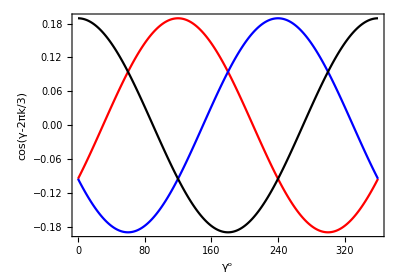

```mathematica
t1=Table[{x,rk[0.3,x,1]},{x,0,360,1}];
t2=Table[{x,rk[0.3,x,2]},{x,0,360,1}];
t3=Table[{x,rk[0.3,x,3]},{x,0,360,1}];
ListLinePlot[{t1,t2,t3},AspectRatio->0.7,Frame->True,Axes->False,PlotStyle->{Red,Blue,Black},FrameLabel->{"γ^o","cos(γ-2πk/3)"},LabelStyle->{15,Black,FontFamily->"Times"}]
```